# Visualisation of neural network predictions for the 2D case

Import relevant neural network predictions files to reproduce result in the manuscript. 

																		Neural network  |  filename 
CNN | 2dcnn_t50.csv
MAgNET | 2dmagnet_t50.csv
Perceiver IO | 2dperceiver_t50.csv

```mathematica
<<AceFEM`;
```

Import the csv file to be visualized, and also get back the force density value from the corresponding nodal force values. (3.229 is the scaling factor applicable to this particular example)

```mathematica
input = Import["cnn_t50.csv"];

(*Retrieve forces applied, true FEM solution and neural network predictions*)
nn=input[[All,2]] ;
fem = input[[All,3]] ;
error = input[[All,4]];
listerror = Partition[error, 2]; 
nodeerror = (Norm/@listerror);(*Nodewise norm of the error*)

(*Get the location and magnitude of the line density force*)
extforce = Total[Partition[input[[All,1]],2]]*3.2291666666666683; 
inds = SparseArray[Partition[input[[All,1]],2]]["NonzeroPositions"][[All,1]];
inds = DeleteDuplicates@*Flatten@inds;
```

Setup the domain as used while generating the dataset.

```mathematica
SMTInputData[];
L=0.8;H=3.2;nx=7;ny=31;
points={{0,0},{L,0},{L,H},{0,H}};
SMTAddDomain["Ω","OL:SEPEQ1DFHYQ1NeoHooke",{"E *"->100,"ν *"->0.3}];
SMTAddMesh[Polygon[points],"Ω","Q1",{nx,ny}];
SMTAnalysis[];
mrest = SMTShowMesh["BoundaryConditions"-> False, "FillElements"->False,"Mesh"->Gray, "ImageSize"->100];
```

Assign true FEM predictions and corresponding neural network predictions.

-Graphics-

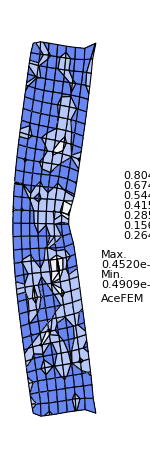

```mathematica
(*Add forces to be visualised*)
SMTAddNaturalBoundary[Line[{SMTNodeData[inds[[1]],"X"],SMTNodeData[inds[[-1]],"X"]}],1->Line[{extforce[[1]]}],2->Line[{extforce[[2]]}]];

(*Assign true FEM solutions. Red mesh*)
SMTNodeData["at",Partition[fem ,2]];
mfem=SMTShowMesh["BoundaryConditions"->True,"DeformedMesh"->True,"Mesh"->Red,"FillElements"->False,"ImageSize"->90];

(*Assign neural network predictions. Blue mesh*)
SMTNodeData["at",Partition[nn ,2]];
mnn=SMTShowMesh["BoundaryConditions"->True,"DeformedMesh"->True,"Mesh"->Blue,"FillElements"->False,"ImageSize"->90];

(*Plot the error of predictions*)
errorplt=SMTShowMesh["BoundaryConditions"->True,"DeformedMesh"->True,"Mesh"->Black,"FillElements"->False,"Field"-> nodeerror,"Contour"->{0.0000264,0.000804,5},"ImageSize"->150] ;

(*Visualize by superimposing solutions*)
Show[mfem,mnn,mrest]  
Show[errorplt]
```